```mathematica
Quiet@Remove@"`*";ClearAll@"`*";
On[Assert]
SetDirectory[NotebookDirectory[]];

Row@{"Suffix: ",suffix="hT"}
lTdts = List["1","0.5","0.1"];
hTdts = List["0.1", "0.05","0.0001"];

a2Data=Import[StringJoin["a2-",suffix,".json"], "RawJSON"];
a1Data0=Import[StringJoin["a1-",suffix,"-", hTdts[[1]],".json"], "RawJSON"];
a1Data1=Import[StringJoin["a1-",suffix,"-",hTdts[[2]],".json"], "RawJSON"];
a1Data2=Import[StringJoin["a1-",suffix,"-",hTdts[[3]],".json"], "RawJSON"];
```

Suffix: hT

Sample sizes: 10000

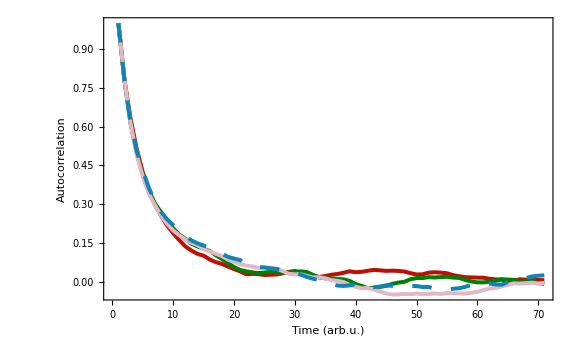

```mathematica
{engyA1n0,engyA1n1,engyA1n2,engyA2} =#["energy_sample"]&/@{a1Data0,a1Data1,a1Data2, a2Data};

Row@{"Sample sizes: ",sampleSize=Length[engyA2]}
Assert@And[
sampleSize==Length[engyA1n0],
sampleSize==Length[engyA1n1],
sampleSize==Length[engyA1n2]
] 
colors = Table[ColorData[58][i],{i,6}];
baseStyle = Directive[Black, FontFamily->"Arial", FontSize->16];
frameStyle = Append[baseStyle, Thickness@0.003];

Show[
ListLinePlot[
CorrelationFunction[#["energy_sample"], {70}]& /@{a1Data0,a1Data1, a1Data2}, PlotRange->All,
PlotStyle->(Directive[ColorData[58][#],Thickness[0.005]]&/@Range[3])], 
ListLinePlot[
CorrelationFunction[a2Data["energy_sample"], {70}], PlotRange->All,
PlotStyle-> {Dashing[Large],Thickness[0.005], colors[[4]]}],
FrameLabel->{
{"Autocorrelation",None},{"Time (arb.u.)",None}
},
FrameTicksStyle->Thickness@0.003,
Epilog->{
Inset[Framed[
LineLegend[{colors[[1]],colors[[2]],colors[[3]], {Dashed, colors[[4]]}},
{"DT, dt=10^-1", "DT, dt= 5×10^-2","DT, dt=10^-4","CT"},
LegendLayout->"Column",LabelStyle->baseStyle
],FrameStyle->Append[baseStyle,Thickness@1],RoundingRadius->5
],Scaled@{0.63,0.63}]
},

BaseStyle->baseStyle,
Axes->False,Frame->{{True,False}, {True, False}},FrameStyle->Append[baseStyle,Thickness@0.004],
ImageSize->Large
]
```